```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[mb2_,q_,T_]:=1/Exp[(√(q^2+mb2))/T-1];
nbd1x[mb2_,q_,T_]:=-1/T nb[mb2,q,T](nb[mb2,q,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
Epi[q_,mp2_]:=(*√(-0.1 q^2+0.01 q^4+mp2)*)√(q^2+mp2);
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B1thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (-nb[mp2,q,T]/(Epi[q,mp2] (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))-(nb[mp2,q,T]+1)/(Epi[q,mp2] (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))+nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q,mp2]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2))+(-1+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q,mp2]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)));
F2B1thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (nb[mp2,q,T]/(Epi[q,mp2] ((-mu+ⅈ p0+Epi[q,mp2])^2-Eq[q,mf2]^2)^2)+(1+nb[mp2,q,T])/(Epi[q,mp2] ((-mu+ⅈ p0-Epi[q,mp2])^2-Eq[q,mf2]^2)^2)+nfa[mf2,q,T,mu]/(2 (-Epi[q,mp2]^2+(-mu+ⅈ p0-Eq[q,mf2])^2) Eq[q,mf2]^3)-((-mu+ⅈ p0-Eq[q,mf2]) nfa[mf2,q,T,mu])/((-Epi[q,mp2]^2+(-mu+ⅈ p0-Eq[q,mf2])^2)^2 Eq[q,mf2]^2)-nfd1xa[mf2,q,T,mu]/(2 (-Epi[q,mp2]^2+(-mu+ⅈ p0-Eq[q,mf2])^2) Eq[q,mf2]^2)-nfd1xf[mf2,q,T,mu]/(2 Eq[q,mf2]^2 (-Epi[q,mp2]^2+(-mu+ⅈ p0+Eq[q,mf2])^2))+((-mu+ⅈ p0+Eq[q,mf2]) (-1+nff[mf2,q,T,mu]))/(Eq[q,mf2]^2 (-Epi[q,mp2]^2+(-mu+ⅈ p0+Eq[q,mf2])^2)^2)+(-1+nff[mf2,q,T,mu])/(2 Eq[q,mf2]^3 (-Epi[q,mp2]^2+(-mu+ⅈ p0+Eq[q,mf2])^2)));
hT[mp2_,ms2_,mf2_,h_,p0_,T_,mu_]:=1/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[-F1B1thr[ms2,mf2,p0,q,T,mu]+2mf2 F2B1thr[ms2,mf2,p0,q,T,mu]],{q,0,5000}]-(Nf^2-1)/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[-F1B1thr[mp2,mf2,p0,q,T,mu]+2mf2 F2B1thr[mp2,mf2,p0,q,T,mu]],{q,0,5000}]
hpiT[mp2_,ms2_,mf2_,h_,p0_,T_,mu_]:=1/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[F1B1thr[ms2,mf2,p0,q,T,mu]],{q,0,5000}]-(Nf^2-1)/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[F1B1thr[mp2,mf2,p0,q,T,mu]],{q,0,5000}]
```

```mathematica
fpidata=Flatten[Import["../renormal/M300.dat"]];
mpdata=Flatten[Import["../mpion_T.dat"]];
msdata=Flatten[Import["../msigma_T.dat"]];
```

```mathematica
data=Table[hT[mpdata[[T]]^2,msdata[[T]]^2,mf2[6.5,fpidata[[T]]/2],6.5,π T,T,0],{T,1,300}];
data2=Table[hpiT[mpdata[[T]]^2,msdata[[T]]^2,mf2[6.5,fpidata[[T]]/2],6.5,π T,T,0],{T,1,300}];
```

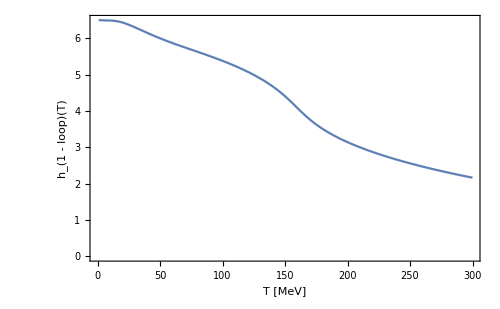

```mathematica
ListLinePlot[{data-data[[1]]+6.5(*,data2-data2[[1]]+6.5*)},PlotRange->All,Frame->True,FrameLabel->{"T [MeV]","h_(1 - loop)(T)"}]
```

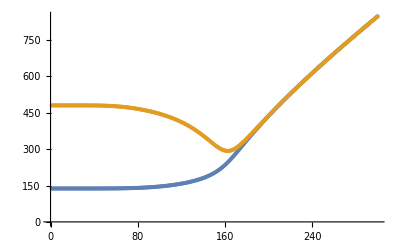

```mathematica
ListPlot[{mpdata,msdata}]
```